```mathematica
(* 27 nearest star systems *)
(* src: https://en.wikipedia.org/wiki/List_of_nearest_stars_and_brown_dwarfs *)
```

```mathematica
dists={4.2441,4.3650,4.3650,5.9577,7.856,8.307,8.659,8.659,8.791,8.791,9.7035,10.2903,10.446,10.7211,11.0074,11.109,11.109,11.109,11.4008,11.4008,11.402,11.402,11.4880,11.4880,11.6182,11.6182,11.6780,11.753,11.869,11.9803,12.1084,12.199,12.496,12.571,12.8294,12.9515,13.0724,13.0724};
RAs="{14h 29m 43.0s,14h 39m 36.5s,14h 39m 35.1s,17h 57m 48.5s,10h 56m 29.2s,11h 03m 20.2s,06h 45m 08.9s,06h 45m 08.9s,01h 39m 01.3s,01h 39m 01.3s,18h 49m 49.4s,23h 41m 54.7s,03h 32m 55.8s,23h 05m 52.0s,11h 47m 44.4s,22h 38m 33.4s,22h 38m 33.4s,22h 38m 33.4s,21h 06m 53.9s,21h 06m 55.3s,07h 39m 18.1s,07h 39m 18.1s,18h 42m 46.7s,18h 42m 46.9s,0h 18m 22.9s,0h 18m 22.9s,08h 29m 49.5s,01h 44m 04.1s,22h 03m 21.7s,03h 35m 59.7s,01h 12m 30.6s,07h 27m 24.5s,02h 53m 00.9s,18h 45m 05.3s,05h 11m 40.6s,21h 17m 15.3s,22h 27m 59.5s,22h 27m 59.5s}";
```

```mathematica
(* TODO: add brown dwarfs *)
```

```mathematica
bdists={6.5029,6.5029,7.26,11.869,11.869,12.571,13.1932}
bRAs="{10h 49m 15.57s,10h 49m 15.57s,08h 55m 10.83s,22h 04m 10.5s,22h 04m 10.5s,18h 45m 02.6s,10h 48m 14.7s}"
```

{6.5029,6.5029,7.26,11.869,11.869,12.571,13.1932}

{10h 49m 15.57s,10h 49m 15.57s,08h 55m 10.83s,22h 04m 10.5s,22h 04m 10.5s,18h 45m 02.6s,10h 48m 14.7s}

```mathematica
nras=ToExpression[StringReplace[RAs," "->"+"]]//.{s->m/60,m->h/60,h->2Pi/24}
nbras=ToExpression[StringReplace[bRAs," "->"+"]]//.{s->m/60,m->h/60,h->2Pi/24}
```

{3.79485,3.83802,3.83791,4.70283,2.86446,2.89435,1.76779,1.76779,0.432064,0.432064,4.92978,6.20426,0.929082,6.04698,3.0881,5.92782,5.92782,5.92782,5.52789,5.52799,2.00408,2.00408,4.89904,4.89906,0.0802052,0.0802052,2.22453,0.454084,5.77425,0.942456,0.316385,1.95219,0.75492,4.90912,1.35995,5.57308,5.88172,5.88172}

{2.83293,2.83293,2.33517,5.7778,5.7778,4.90893,2.8285}

```mathematica
iunred={2,3,7,8,13,19,20,21,22,28,29}
ired=Complement[Range[Length[dists]],iunred]
```

{2,3,7,8,13,19,20,21,22,28,29}

{1,4,5,6,9,10,11,12,14,15,16,17,18,23,24,25,26,27,30,31,32,33,34,35,36,37,38}

```mathematica
ListPolarPlot[{Transpose[{nras,dists}][[iunred]],Transpose[{nras,dists}][[ired]],Transpose[{nbras,bdists}]},PlotRange->{{-13.2,13.2},{-13.2,13.2}},PlotStyle->{{RGBColor[1,.8,0],PointSize[.02]},{Red,PointSize[.01]},{Black,PointSize[.005]}},PlotTheme->{"Scientific","Grid"}]
(* 27 star systems within 13.1 ly *)
```

-Graphics-

```mathematica
(* compare https://apod.nasa.gov/apod/ap010318.html below *)
```

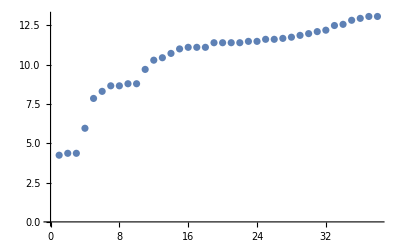

```mathematica
ListPlot[dists]
```

```mathematica
ListPolarPlot[Select[#,#[[2]]<10&]&/@{Transpose[{nras,dists}][[iunred]],Transpose[{nras,dists}][[ired]],Transpose[{nbras,bdists}]},PlotRange->{{-10,10},{-10,10}},PlotStyle->{{RGBColor[1,.8,0],PointSize[.02]},{Red,PointSize[.01]},{Black,PointSize[.005]}},PlotTheme->{"Scientific","Grid"}]
(* closest 10 stars 
 = closest 10 s/bd systems 
= within 10 ly *)
```

-Graphics-

```mathematica
(* compare https://steemit.com/steemstem/@terrylovejoy/the-alpha-centauri-star-system below *)
```

```mathematica
(* also: *) -Graphics-
```

```mathematica
(* and also https://web.archive.org/web/20090613110046if_/http://www.jointquest.com/jointquest-old/NationalGeographicTheUniverseMap.jpg *)
```